## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/manipulate/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.210828 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Mar 30, 2020, time: 09:19:28

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/manipulate/the hell with this.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.210828 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
isize=ImageSize->6 72;
```

```mathematica
ipad=ImagePadding->{{Automatic,5},{Automatic,Automatic}};
```

#### functions

#### substitutions

#### modules

## 2 Fourier

```mathematica
(* Mercury MoM output *)
meanRCS=Import[dirData<>"rcs-values.dat"];
```

```mathematica
ν=30;d=14;
```

```mathematica
meanRCS=Import["rcs-values.dat"];
(* pointer to data file *)
index=ν-2;
(* wavelegnth in meters *)
λ=Round[𝕔/(ν 1000000)];
(* grab rcs at specific wavelength *)
rcs=meanRCS[[index]];
(* number of data points *)
Θ=Table[
k π/180
,{k,-180,180}];
m=Length[Θ];
(* center on nose (yaw angle α = 90 ) *)
σ=RotateLeft[rcs,180];
(* characterize variation for plot range *)
mx=Max[σ];
mn=Min[σ];
Λ=1.1;
{top,bot}={1.1mx,0.9mn};
(* plot subtitles *)
subtitle="ν = "<>ToString[ν]<>" MHz";
subtitle=subtitle<>", λ = "<>ToString[λ]<>" m";
(* scatter plot of data points *)
z={Θ,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
(* assemble linear system *)
avector=Table[Cos[j θ],{j,0,d}];
A=Table[
Simplify[avector/.θ->Θ[[k]]]
,{k,m}];
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
(* approximation function *)
Clear[f];
f[θ_]=c.avector;
(* approximation vector *)
F=f[θ]/.θ->Θ;
(* residual error *)
r=σ-F;
R={Θ,r}ᵀ;
(* total error *)
r2=r.r;
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
(* signal to noise *)
γ=Last[c]/Last[ϵ];
(* function *)
g001=Plot[f[θ],{θ,-π,π},
Frame->True,
FrameTicks->fticks,
PlotRange->All,
PlotStyle->{Opacity[0.25],Blue}];
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>subtitle,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize];
(* compare data to fit *)
dsubtitle=subtitle<>", d = "<>ToString[d];
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"<>lf<>dsubtitle],
FrameLabel->{sty["Yaw angle, α"],sty["Mean total RCS, <σ_T>"]},
FrameTicks->fticks,
PlotRange->{bot,top},
isize,ipad];
(* residual error *)
gb=ListPlot[R,
Frame->True,
FrameTicks->fticks,
FrameLabel->{sty["Yaw angle, α"],sty["Residual error"]},
(* PlotRange->Λ{-1,1}, *)
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"<>lf<>dsubtitle],
isize,ipad];
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>subtitle,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize];
(* amplitudes with errors *)
ebars=Table[
{k-1,Around[c[[k]],ϵ[[k]]]}
,{k,Length[c]}];
gebars=ListPlot[ebars,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[{k,Subscript["a",k]},{k,0,Length[ebars]}],Automatic}},
PlotLabel->"Amplitudes with errors for d = "<>ToString[d]<>lf<>subtitle,
PlotStyle->Blue,
PlotRange->{{-0.5,d+0.5},Full},
isize,ipad];
(* group plots *)
gout=GraphicsGrid[{{ga,gb},{gbars,gebars}},
ImageSize->12 72]
```

## 3

```mathematica
tresExport["fourier-worst-30-14",gout];
```

## 4 Taylor

```mathematica
(* Mercury MoM output *)
meanRCS=Import[dirData<>"rcs-values.dat"];
```

```mathematica
α=180;d=4;
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{28.,462.,9450.,216216.,5.27398×10^6},{462.,9450.,216216.,5.27398×10^6,1.33987×10^8},{9450.,216216.,5.27398×10^6,1.33987×10^8,3.50093×10^9},{216216.,5.27398×10^6,1.33987×10^8,3.50093×10^9,9.33725×10^10},{5.27398×10^6,1.33987×10^8,3.50093×10^9,9.33725×10^10,2.52962×10^12}} may contain significant numerical errors.

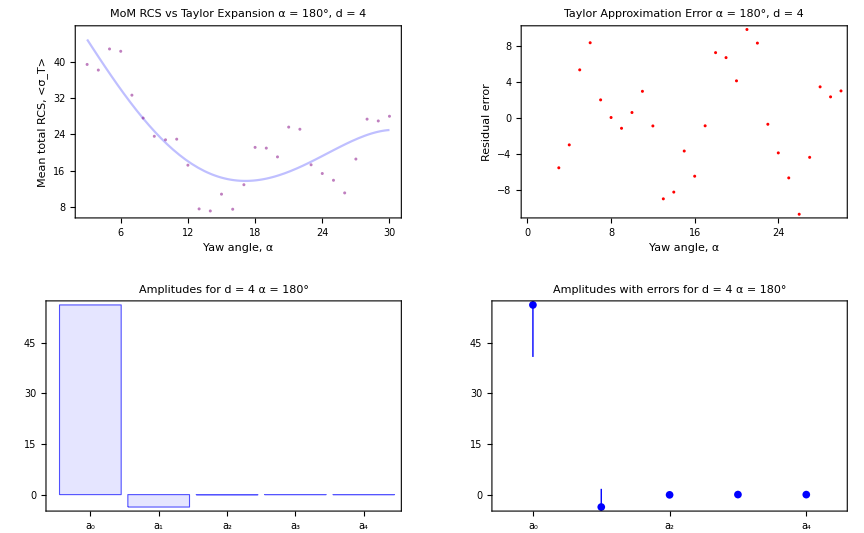

```mathematica
meanRCS=Import["rcs-values.dat"];
(* pointer to data file *)
index=α;
(* grab rcs at specific wavelength *)
rcs=meanRCSᵀ[[index]];
(* number of data points *)
ν=Range[3,30];
m=Length[ν];
(*  *)
σ=rcs;
(* characterize variation for plot range *)
mx=Max[σ];
mn=Min[σ];
Λ=1.1;
{top,bot}={1.1mx,0.9mn};
(* plot subtitles *)
subtitle="α = "<>ToString[α]<>"°";
(* scatter plot of data points *)
z={ν,σ}ᵀ;
g000=ListPlot[z,PlotStyle->{Purple,Opacity[0.5],PointSize[0.005]}];
(* assemble linear system *)
xvector=Table[x^j,{j,0,d}];
A=Table[
Simplify[xvector/.x->ν[[k]]]
,{k,m}];
(* compute Fourier-Bessel coefficients *)
c=LeastSquares[A,σ];
(* approximation function *)
Clear[f];
f[x_]=c.xvector;
(* approximation vector *)
F=f[x]/.x->ν;
(* residual error *)
r=σ-F;
R={ν,r}ᵀ;
(* total error *)
r2=r.r;
(* uncertainty propagation *)
ϵ=√(r2/(m-(d+1))Diagonal[Inverse[A†.A//N]]);
(* signal to noise *)
γ=Last[c]/Last[ϵ];
(* function *)
g001=Plot[f[ν],{ν,3,30},
Frame->True,
PlotRange->All,
PlotStyle->{Opacity[0.25],Blue}];
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d],
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize];
(* compare data to fit *)
dsubtitle=subtitle<>", d = "<>ToString[d];
ga=Show[{g001,g000},
Axes->False,
PlotLabel->"MoM RCS vs Taylor Expansion"<>lf<>dsubtitle,
FrameLabel->{"Yaw angle, α","Mean total RCS, <σ_T>"},
PlotRange->{{2.5,30.5},{bot,top}},
isize,ipad];
(* residual error *)
gb=ListPlot[R,
Frame->True,
FrameLabel->{"Yaw angle, α","Residual error"},
(* PlotRange->Λ{-1,1}, *)
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->"Taylor Approximation Error"<>lf<>dsubtitle,
isize,ipad];
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>subtitle,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize];
(* amplitudes with errors *)
ebars=Table[
{k-1,Around[c[[k]],ϵ[[k]]]}
,{k,Length[c]}];
gebars=ListPlot[ebars,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[{k,Subscript["a",k]},{k,0,Length[ebars]}],Automatic}},
PlotLabel->"Amplitudes with errors for d = "<>ToString[d]<>lf<>subtitle,
PlotStyle->Blue,
PlotRange->{{-0.5,d+0.5},Full},
isize,ipad];
(* group plots *)
gout=GraphicsGrid[{{ga,gb},{gbars,gebars}},
ImageSize->12 72]
```

## export

```mathematica
tresExport["taylor-worst-180-4",gout];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```